```mathematica
(************************************************************)
(***Динамика сферических роботов на основе параллельных механизмов***)
(************************************************************)
```

```mathematica
(*Вспомогательные функции*)
```

```mathematica
(*Кососимметричная матрица из вектора*)
skewSymmetricMatrix[vec_]:=With[{x=vec[[1]],y=vec[[2]],z=vec[[3]]},{{0,-z,y},{z,0,-x},{-y,x,0}}];

(*Вращение по преобразованной формуле Родригеса*)
(*
rotateRodrigues[vec_,ang_]:=Cos[vecNorm[ang]]*vec+Sinc[vecNorm[ang]]*Cross[ang,vec]+1/2*Sinc[vecNorm[ang]/2]^2*Dot[ang,vec]*ang;
*)
rodriguesMatrix[ang_]:=With[{angMagn=vecNorm[ang]},With[{cosAM=Cos[angMagn],sincAM=Sinc[angMagn],sincAM2Sq2=1/2*Sinc[1/2*angMagn]^2},{{cosAM+ang[[1]]^2*sincAM2Sq2,
ang[[1]]*ang[[2]]*sincAM2Sq2+ang[[3]]*sincAM,
ang[[1]]*ang[[3]]*sincAM2Sq2-ang[[2]]*sincAM},
{ang[[1]]*ang[[2]]*sincAM2Sq2-ang[[3]]*sincAM,
cosAM+ang[[2]]^2*sincAM2Sq2,
ang[[2]]*ang[[3]]*sincAM2Sq2+ang[[1]]*sincAM},
{ang[[1]]*ang[[3]]*sincAM2Sq2+ang[[2]]*sincAM,
ang[[2]]*ang[[3]]*sincAM2Sq2-ang[[1]]*sincAM,
cosAM+ang[[3]]^2*sincAM2Sq2}}]];
rotateRodrigues[vec_,ang_]:=vec.rodriguesMatrix[ang];

(*Момент инерции*)
momentOfInertia[coef_,mass_,radius_]:=(coef*mass*radius^2)*IdentityMatrix[3];
(*Теорема Гюйгенса-Штейнера*)
parallelAxisInertia[inertia_,mass_,vec_]:=inertia-mass*MatrixPower[skewSymmetricMatrix[vec],2]; 

(*Момент силы*)
torque[axisPoint_,forcePoint_,force_]:=Cross[forcePoint-axisPoint,force];
```

```mathematica
(*Вспомогательные величины*)
```

```mathematica
(*Гравитация*)
gravityField={0,0,-g};
gravityForce[mass_]:=mass*gravityField;
```

```mathematica
(*Точка контакта с поверхностью в невращающейся системе координат робота*)
groundContactPoint=sphereRadius*{Sin[groundAngle],0,-Cos[groundAngle]};
```

```mathematica
(*Переменные состояния робота*)
```

```mathematica
(*Моменты инерции корпуса и рабочего органа относительно свох центров масс*)
sphereMomentOfIntertia=momentOfInertia[sphereInertiaCoef,sphereMass,sphereRadius];
endEffectorMomentOfIntertia=momentOfInertia[endEffectorInertiaCoef,endEffectorMass,endEffectorRadius];

robotTotalMomentOfIntertia=sphereMomentOfIntertia+endEffectorMomentOfIntertia;
```

```mathematica
(*Угловые положение, скорость и ускорение корпуса робота*)
bodyAngularPosition={bAngPx[t],bAngPy[t],bAngPz[t]};
bodyAngularVelocity={bAngPx'[t],bAngPy'[t],bAngPz'[t]};
bodyAngularAcceleration={bAngPx''[t],bAngPy''[t],bAngPz''[t]};

problem2D[arr_]:={arr[[2]]};
problem3D[arr_]:=arr;

(*Относительное положение, скорость и ускорение рабочего органа и центра тяжести робота в невращающейся системе координат робота*)
endEffectorDisplacementInNCS={nx,ny,nz};
endEffectorVelocityInNCS={nvx,nvy,nvz};
endEffectorAccelerationInNCS={nax,nay,naz};
```

```mathematica
(*Вязкое трение*)
viscousFrictionTorque=-bodyAngularVelocity*{rollFriction,rollFriction,torsionFriction};

(*Полный вращательный момент, действующий на робота, относительно точки касания корпуса с поверхностью*)
robotTotalTorque=torque[groundContactPoint,endEffectorDisplacementInNCS,gravityForce[endEffectorMass]]+torque[groundContactPoint,nullVector,gravityForce[sphereMass]]+viscousFrictionTorque;
```

```mathematica
(*Система уравнений динамики*)
robotDynamicsEquations=Thread[(robotTotalMomentOfIntertia.bodyAngularAcceleration+Cross[bodyAngularVelocity,robotTotalMomentOfIntertia.bodyAngularVelocity]+Cross[groundContactPoint,sphereMass*Cross[bodyAngularAcceleration,groundContactPoint]]+Cross[endEffectorDisplacementInNCS-groundContactPoint,endEffectorMass*endEffectorAccelerationInNCS])==robotTotalTorque]//FullSimplify
```

{endEffectorMass (g+naz) ny+rollFriction bAngPx'[t]+(endEffectorInertiaCoef endEffectorMass endEffectorRadius^2+sphereInertiaCoef sphereMass sphereRadius^2+sphereMass sphereRadius^2 Cos[groundAngle]^2) bAngPx''[t]+sphereMass sphereRadius^2 Cos[groundAngle] Sin[groundAngle] bAngPz''[t]==endEffectorMass nay (nz+sphereRadius Cos[groundAngle]),endEffectorMass nax (nz+sphereRadius Cos[groundAngle])+(endEffectorMass (g+naz)+g sphereMass) sphereRadius Sin[groundAngle]+rollFriction bAngPy'[t]+(endEffectorInertiaCoef endEffectorMass endEffectorRadius^2+(1+sphereInertiaCoef) sphereMass sphereRadius^2) bAngPy''[t]==endEffectorMass (g+naz) nx,torsionFriction bAngPz'[t]+endEffectorMass (nay nx-nax ny-nay sphereRadius Sin[groundAngle]+endEffectorInertiaCoef endEffectorRadius^2 bAngPz''[t])+sphereMass sphereRadius^2 (Cos[groundAngle] Sin[groundAngle] bAngPx''[t]+(sphereInertiaCoef+Sin[groundAngle]^2) bAngPz''[t])==0}

```mathematica
(*Преобразования координат при переходе из вращающейся системы отсчета в невращающуюся и обратно*)
switchFromRotatingToNonrotatingCS[points_]:=Map[rotateRodrigues[#,bodyAngularPosition]&,points];
switchFromNonrotatingToRotatingCS[points_]:=Map[rotateRodrigues[#,-bodyAngularPosition]&,points];
```

```mathematica
(*Значения динамических параметров модели*)
robotDynamicsParametersValues={g->9.81,groundAngle->0,sphereInertiaCoef->2/3,endEffectorInertiaCoef->2/5,sphereMass->0.1,endEffectorMass->1,rollFriction->0.0,torsionFriction->0.0};
```

```mathematica
(*******************************************************************************************)
```

```mathematica
robotEndEffectorMovementStrategy[displ_,vel_,acc_]:=Thread[Join[endEffectorDisplacementInNCS,endEffectorVelocityInNCS,endEffectorAccelerationInNCS]->Join[displ,vel,acc]];

robotEndEffectorMovementStrategyByDisplacementOnly[displ_]:=Module[{vel=Dt[displ,t],acc=Dt[displ,{t,2}]},robotEndEffectorMovementStrategy[displ,vel,acc]];
```

```mathematica
maxEndEffectorDisplacementMagnitude=0.25;

(*Экономное rho-only 2D-движение*)
polePointTheta=-bAngPy[t];

endEffectorDisplacementMagnitudeRule[theta_]:=maxEndEffectorDisplacementMagnitude*(0.5*(1-0.7^2))/(1-0.7*Cos[theta]);

endEffectorRhoOnlyMovementStrategy2D=robotEndEffectorMovementStrategyByDisplacementOnly[cartesian[{endEffectorDisplacementMagnitudeRule[polePointTheta],0,polePointTheta}]]//FullSimplify;
```

```mathematica
(*Начальные условия*)
robotInitialBodyAngularVelocityValue={0,10,0};

robotDynamicsInitialConditions=Transpose[{MapThread[Equal,{bodyAngularPosition/.t->0,nullVector}],MapThread[Equal,{bodyAngularVelocity/.t->0,robotInitialBodyAngularVelocityValue}]}];
```

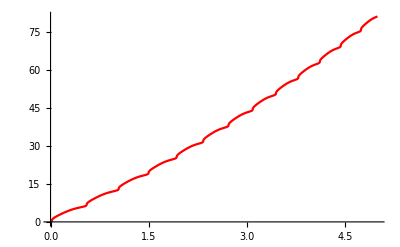

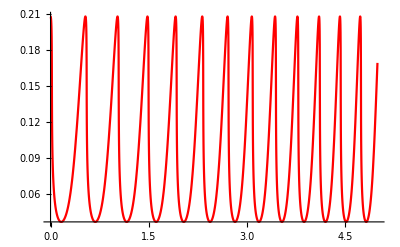

```mathematica
(*Численное решение системы уравнений для заданной стратегии движения*)
currentEndEffectorMovementStrategy=endEffectorRhoOnlyMovementStrategy2D;
considerProblemDimensionality=problem2D;

modelLifeTime=5;
currentRobotDynamicsSolution=NDSolve[Join[considerProblemDimensionality[robotDynamicsEquations]/.robotDynamicsParametersValues/.robotParametersValues/.currentEndEffectorMovementStrategy/.robotParametersValues//FullSimplify//Chop,Flatten[considerProblemDimensionality[robotDynamicsInitialConditions]]],considerProblemDimensionality[bodyAngularPosition],{t,0,modelLifeTime}];

Plot[Evaluate[considerProblemDimensionality[bodyAngularPosition]/.currentRobotDynamicsSolution],{t,0,modelLifeTime},PlotStyle->considerProblemDimensionality[{Green,Red,Blue}]]

Plot[endEffectorDisplacementMagnitudeRule[polePointTheta/.currentRobotDynamicsSolution],{t,0,modelLifeTime},PlotStyle->considerProblemDimensionality[{Green,Red,Blue}]]
```